```mathematica
Solve[1.4x/(.2+x)==.1x/(.8+4x),x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.}}

x1’=-1.4x1+.2x2+x1x2
x2’=.1x1-.8x2-4x1x2

g1= f1(x1,x2)+x1
g2= f2(x1,x2)+x2

```mathematica
A={{a+.4 ,.2},{.1,a-.2}}
```

{{0.4+a,0.2},{0.1,-0.2+a}}

```mathematica
Solve[Det[A]==0,a]
```

{{a→-0.431662},{a→0.231662}}

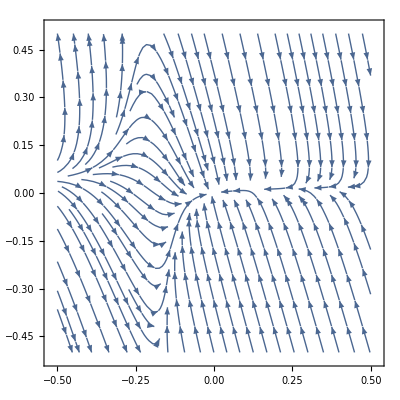

```mathematica
StreamPlot[{-.14x+.2y+x*y,.1x-.8y-4x*y},{x,-.5,.5},{y,-.5,.5}]
```

```mathematica
A:={{.4 ,.2},{c,.2}}
```

```mathematica
MatrixForm[{{.4 ,.2},{c,.2}}]
```

(0.4 | 0.2
c | 0.2)

```mathematica
Eigenvalues[A]
```

{0.1 (3.-√(1.+20. c)),0.1 (3.+√(1.+20. c))}

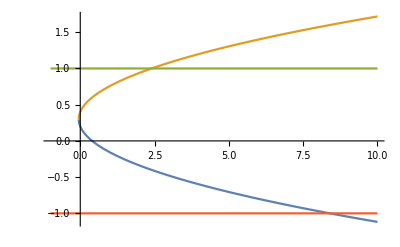

```mathematica
Plot[{0.1 (3.0000000000000004-√(1.0000000000000018+20. c)),0.1 (3.0000000000000004+√(1.0000000000000018+20. c)),1,-1},{c,-1,10}]
```

```mathematica
Eigenvectors[A]
```

{{-(0.1 (-1.+1. √(1.+20. c)))/c,1.},{(0.1 (1.+1. √(1.+20. c)))/c,1.}}

```mathematica
Solve[Det[A[c]]==0,a]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→0.1 (-1.-1. √(9.+20. c))},{a→0.1 (-1.+√(9.+20. c))}}